### Description

To find a weight network generator of IIT model with lowest bias.

### Conclusion

The Uniform Distribution seems have the lowest bias.

#### Normal Distribution σ = 1

```mathematica
transitions=Import[FileNameJoin[{NotebookDirectory[],"data","transitions.csv"}]]⟦2;;⟧ᵀ⟦2;;⟧ᵀ;
```

```mathematica
RTrans=DimensionReduce[transitions,2];
```

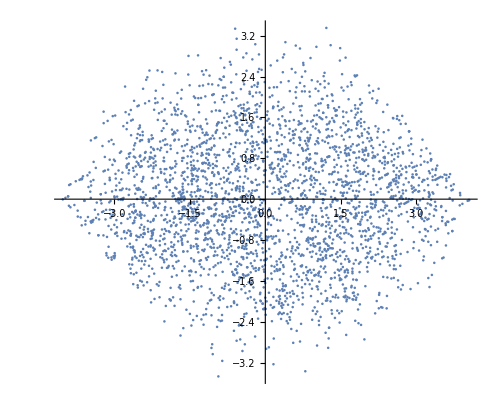

```mathematica
ListPlot[RandomSample[RTrans,3000],AspectRatio->Automatic]
```

```mathematica
RandomSample[transitions,10]
```

{{1,3,7,3,7,3,7,3},{0,3,7,7,4,2,4,7},{4,6,0,2,5,7,5,4},{7,7,6,7,2,2,6,6},{6,1,0,1,5,5,5,1},{2,3,5,7,5,7,5,7},{2,1,7,3,6,5,6,7},{3,0,2,2,6,0,2,2},{4,4,5,4,7,7,5,5},{4,0,7,2,1,0,3,1}}

#### Uniform Distribution (-1,1)

```mathematica
transitionsu=Import[FileNameJoin[{NotebookDirectory[],"data","transitionsu.csv"}]]⟦2;;⟧ᵀ⟦2;;⟧ᵀ;
```

```mathematica
RTransU=DimensionReduce[transitionsu,2];
```

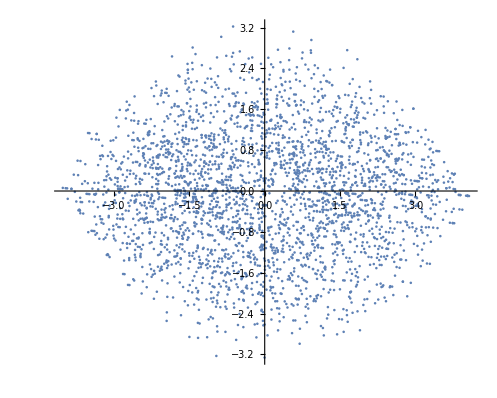

```mathematica
ListPlot[RandomSample[RTransU,3000],AspectRatio->Automatic]
```

```mathematica
Length[Tally[transitionsu]]/Length[transitionsu]//N
```

0.9238

```mathematica
Length[Tally[transitions]]/Length[transitions]//N
```

0.9275

#### Laplace Distribution (0,1)

```mathematica
transitionsl=Import[FileNameJoin[{NotebookDirectory[],"data","transitionsl.csv"}]]⟦2;;⟧ᵀ⟦2;;⟧ᵀ;
```

```mathematica
RTransL=DimensionReduce[transitionsl,2];
```

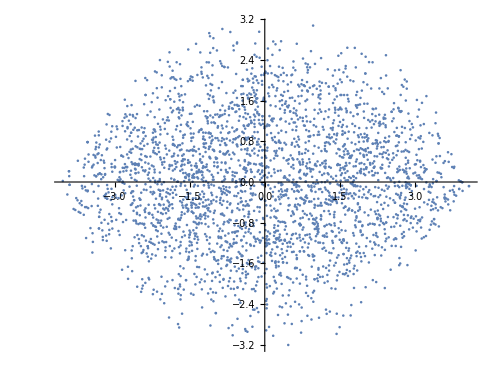

```mathematica
ListPlot[RandomSample[RTransL,3000],AspectRatio->Automatic]
```

```mathematica
Length[Tally[transitionsl]]/Length[transitionsl]//N
```

0.9143

```mathematica
Length[Tally[transitionsu]]/Length[transitionsu]//N
```

0.7364

```mathematica
Length[Tally[transitions]]/Length[transitions]//N
```

0.7024